# Wechselspannung

ω = 2ℼf

```mathematica
f = {137.0,733,35.46,4.080*10^(3),4.120*10^(3),480.0*10^(3),990*10^(3)}
```

{137.,733,35.46,4080.,4120.,480000.,990000}

```mathematica
sf = {0.5,1,0.03,5,500,1000,8000}
```

{0.5,1,0.03,5,500,1000,8000}

```mathematica
ue = {3.50,3.40,3.41,3.40,3.40,3.20,2.72}
```

{3.5,3.4,3.41,3.4,3.4,3.2,2.72}

```mathematica
sue = {0.1,0,0.01,0.01,0.01,0.01,0.02}
```

{0.1,0,0.01,0.01,0.01,0.01,0.02}

```mathematica
ua = {461*10^(-3),196*10^(-3),1.42,180*10^(-3),184*10^(-3),177*10^(-3),163*10^(-3)} //N
```

{0.461,0.196,1.42,0.18,0.184,0.177,0.163}

```mathematica
sua = {10^(-3),0,0.01,2*10^(-3),10^(-3),10^(-3),10^(-3)}
```

{1/1000,0,0.01,1/500,1/1000,1/1000,1/1000}

## Aufgabe 3

C = 100nF

R = 100kΩ

```mathematica
c = 100*10^(-9)
```

1/10000000

```mathematica
R=100*10^3
```

100000

```mathematica
a=Table[{f[[i]],Abs[ue[[i]]/ua[[i]]]/(2π*f[[i]]*c)}, {i, 1, Length[f]}]
```

{{137.,88199.6},{733,37665.1},{35.46,107782.},{4080.,7368.28},{4120.,7138.12},{480000.,59.9454},{990000,26.8266}}

```mathematica
b=Table[{f[[i]],Sqrt[1+(2π*f[[i]]*R*c)^2]/(2π*f[[i]]*c)}, {i, 1, Length[f]}]//N
```

{{137.,100673.},{733.,100024.},{35.46,109611.},{4080.,100001.},{4120.,100001.},{480000.,100000.},{990000.,100000.}}

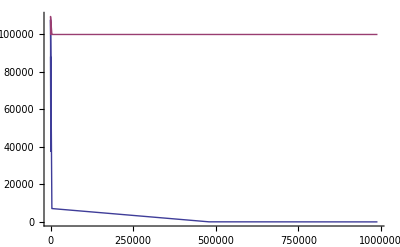

```mathematica
ListPlot[{a,b}, Joined->True]
```